```mathematica
(*Compute the repo root from the notebook location*)
repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;
```

```mathematica
{r,df,db,ch2}.Sigma.{1,m,t,td}
```

-ch2+(-db+df) m+(db+2 df) t-r td

```mathematica
Factor[64-80 u+153 u^2]
```

64-80 u+153 u^2

```mathematica
Simplify@Abs[8/153 (5-8 ⅈ √2)]
```

8/(3 √17)

```mathematica
points=Table[8/153 (5-8 ⅈ √2)+1/10Exp[I x Degree], {x, 60, 150, 10}];
```

{{u→-8/9},{u→-8/9},{u→8/153 (5-8 ⅈ √2)},{u→8/153 (5+8 ⅈ √2)}}

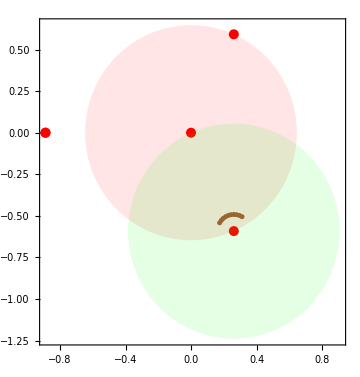

```mathematica
Solve[MirrorCurveDelta2[-27/256,u]==0, u]
Graphics[{PointSize[.02],Red,Point[ReIm/@Join[u/.%,{0}]], Opacity[.1,Red],Disk[ReIm[0],8/(3 √17)], Opacity[.1,Green], Disk[ReIm[8/153 (5-8 ⅈ √2)],8/(3 √17)], PointSize[.01],Opacity[1,Brown], Point[ReIm/@points]},Frame->True,Axes->True,ImageSize->Medium]
```

```mathematica
FullSimplify[Series[MirrorCurveJ2[-27/256,u], {u,8/153 (5-8 ⅈ √2),2}]]
```

(2048 ⅈ (6976 ⅈ+11369 √2))/(5688387 (u-8/153 (5-8 ⅈ √2)))+(16 (15427825+3424 ⅈ √2))/334611+((-434574656-708231089 ⅈ √2) (u-8/153 (5-8 ⅈ √2)))/34992+((-5229553881691+3968930012384 ⅈ √2) (u-8/153 (5-8 ⅈ √2))^2)/13436928+O[u-8/153 (5-8 ⅈ √2)]^3

```mathematica
pf1=FullSimplify[Collect[FullSimplify[PicardFuchs2[f[u],-27/256,u]], {f[u],f'[u],f''[u]}]/.{f->Function[u, F[u-8/153 (5-8 ⅈ √2)]]}/.{u->z+8/153 (5-8 ⅈ √2)}]
```

(306 (-2048 (235939 ⅈ+103816 √2)+153 z (256 (-76977 ⅈ+27824 √2)+153 z (32 (-1333 ⅈ+6000 √2)+153 (1000 ⅈ+768 √2+459 ⅈ z) z))) F'[z])/((40 ⅈ+64 √2+153 ⅈ z)^2 (176 ⅈ+64 √2+153 ⅈ z)^2 (128 √2+153 ⅈ z) z)-(18 (-8192 (24 ⅈ+√2)+17 z (128 (-393 ⅈ+500 √2)+153 (500 ⅈ+576 √2+459 ⅈ z) z)) F''[z])/((40 ⅈ+64 √2+153 ⅈ z) (176 ⅈ+64 √2+153 ⅈ z) (128 √2+153 ⅈ z) z)+F^(3)[z]

```mathematica
currentOrder=1;
A0=z;
coeffList={};
MaxTerms=30;
```

```mathematica
Monitor[Do[
var=Symbol["a"<>ToString[currentOrder+1]];
A0=A0+var z^(currentOrder+1);
limit=Limit[z^(2-currentOrder)(pf1/.F->Function[z,Evaluate[A0]]), z->0];
sol=FullSimplify[Solve[limit==0,var]];
A0=A0/.First[sol];
AppendTo[coeffList, var/.First[sol]];
currentOrder=currentOrder+1;
, {i, MaxTerms}], ProgressIndicator[i/MaxTerms]]
```

```mathematica
N[Abs[(Last[coeffList])^(-1/currentOrder)],50]
```

0.70143210077490743622878747975553682307352915158096

```mathematica
N[Abs[8/153 (5-8 ⅈ √2)]]
```

0.646762

```mathematica
curr=1;
A1=0;
coeffList2={};
MaxTerms=15;
```

```mathematica
powers=z^Range[2,MaxTerms];
```

```mathematica
Monitor[Do[
var=Symbol["b"<>ToString[curr+1]];
limit=Limit[z^(2-curr)(pf1/.F->Function[z,Evaluate[Log[z](z+coeffList[[;;curr]].powers[[;;curr]])+A1+var z^(curr+1)]]),z->0];
sol=Solve[limit==0,var];
A1=A1+FullSimplify[var z^(curr+1)/.First[sol]];
AppendTo[coeffList2, FullSimplify[var/.First[sol]]];
curr=curr+1;
, {i, MaxTerms}], ProgressIndicator[i/MaxTerms]]
```

```mathematica
Phi1=z+coeffList[[;;MaxTerms]].powers[[;;MaxTerms]];
Phi2=Log[z]Phi1+A1;
```

```mathematica
Series[pf1/.F->Function[z,Evaluate[Phi1]], {z,0,MaxTerms-2}]
```

O[z]^14

```mathematica
Series[pf1/.F->Function[z,Evaluate[Phi2]], {z,0,MaxTerms-2}]
```

O[z]^14

```mathematica
Solve[KerrDoranElFromb[b]==-27/256,b]
Simplify[KerrDoranUrFromb[b]/.%]
```

{{b→1},{b→1},{b→1},{b→1},{b→},{b→},{b→},{b→}}

{-8/9,-8/9,-8/9,-8/9,8/153 (5-8 ⅈ √2),8/153 (5+8 ⅈ √2),8/153 (5+8 ⅈ √2),8/153 (5-8 ⅈ √2)}

```mathematica
b0=;
```

```mathematica
points
```

{8/153 (5-8 ⅈ √2)+1/10 ⅇ^(60 ⅈ °),8/153 (5-8 ⅈ √2)+1/10 ⅇ^(70 ⅈ °),8/153 (5-8 ⅈ √2)+1/10 ⅇ^(80 ⅈ °),8/153 (5-8 ⅈ √2)+1/10 ⅇ^(90 ⅈ °),8/153 (5-8 ⅈ √2)+1/10 ⅇ^(100 ⅈ °),8/153 (5-8 ⅈ √2)+1/10 ⅇ^(110 ⅈ °),8/153 (5-8 ⅈ √2)+1/10 ⅇ^(120 ⅈ °),8/153 (5-8 ⅈ √2)+1/10 ⅇ^(130 ⅈ °),8/153 (5-8 ⅈ √2)+1/10 ⅇ^(140 ⅈ °),8/153 (5-8 ⅈ √2)+1/10 ⅇ^(150 ⅈ °)}

```mathematica
N[fT[-27/256,points[[1]],450,6],50]
```

0.01395739453772066108081509743149555767627193010897+0.19139413413021919109265763118782299168359825164888 ⅈ

```mathematica
N[fTD[-27/256,points[[1]],450,6],50]
```

-0.02385785484379432687255268645692223348580159118817+0.038944200517745179575824000548592799049282153471391 ⅈ

```mathematica
N[Log[-27/256]/3/(2Pi I)]
```

0.166667+0.119331 ⅈ

```mathematica
ttable=Table[N[fT[-27/256,p,450,6],50], {p, points}];
tdtable=Table[N[fTD[-27/256,p,450,6],50], {p, points}];
```

```mathematica
N[a+b Log[-27/256]/3/(2Pi I)+c Phi1+d Phi2/.z->points-8/153 (5-8 ⅈ √2),50];
lhs=%-ttable;
```

```mathematica
sol=First[Solve[Thread[lhs[[{1,3,6}]]==0],{a,c,d}]]
```

{a→(-0.01363180547108507615805059758677360659402588282+0.16569532254606235627125864609221678837125933634 ⅈ)-(0.16666666666666666666666666666666666666666666667+0.1193312239205055688632062684312975421304002217 ⅈ) b,c→(0.229419128979544148222207403853877692094605791+0.0517397481746165682867473147707298299850326039 ⅈ)+(0.+0. ⅈ) b,d→(-0.0628807128328707319308959215124094398615047099+0.025605488140369114041658174016110096281950091 ⅈ)+(0.+0. ⅈ) b}

```mathematica
Chop[c/.sol]
```

0.229419128979544148222207403853877692094605791+0.0517397481746165682867473147707298299850326039 ⅈ

```mathematica
Chop[d/.sol]
```

-0.0628807128328707319308959215124094398615047099+0.025605488140369114041658174016110096281950091 ⅈ

```mathematica
FullSimplify[(b^2+b+1)(b^2+4b+1)^2/(1-b)/(b+1)^5/.{b->b0}]
N[%/4/Pi^2]
```

-1/16 √(1316-(1817 ⅈ)/(√2))

-0.0628807+0.0256055 ⅈ

```mathematica
B0=-1/16 √(1316-(1817 ⅈ)/(√2));
N[%]
```

-2.48243+1.01086 ⅈ

```mathematica
m0=Log[-27/256]/3/(2Pi I);
```

```mathematica
Q0=-2Pi(2Pi KerrDoranQ[b0]+Pi/6);
```

```mathematica
B1=FullSimplify[Log[(b^3 (b^2+b+1) (b^2+4 b+1)^2)/(1-b^2)^6]/.{b->b0}];
```

```mathematica
{B0 Phi1, B0 Phi2+B0 B1 Phi1+Q0}
```

```mathematica
N[a+b(B0 Phi1/(4Pi^2))+c(B0 Phi2+B0 B1 Phi1+Q0)/(4Pi^2)/.z->points-8/153 (5-8 ⅈ √2),50];
lhs=%-ttable;
```

```mathematica
sol=First[Solve[Thread[lhs[[{1,3,6}]]==0],{a,b,c}]]
```

{a→0.249999885897328814320942060847849627565101228882+0.1193311453119717302591546930258152812135520996233 ⅈ,b→-1.000002153740584376540706327649381642397171990338-3.14159280564084448825045518095565441919893128848 ⅈ,c→0.9999996398961416810812092983131168127714110189862-3.750239392137625020441543554145765272637618935272×10^-7 ⅈ}

```mathematica
N[a+b(B0 Phi1/(4Pi^2))+c(B0 Phi2+B0 B1 Phi1+Q0)/(4Pi^2)/.z->points-8/153 (5-8 ⅈ √2),50];
lhs=%-tdtable;
```

```mathematica
sol=First[Solve[Thread[lhs[[{1,3,6}]]==0],{a,b,c}]]
```

{a→-1.932569893460855193341624493557253803362112809985×10^-8-2.905685093505576973717461031342638845734023459811×10^-8 ⅈ,b→-4.893823395827432062385842924450780587062592013359×10^-7-6.283185544244929518392134466377295012256965752201 ⅈ,c→-4.911440388058343580942113500052902764542002562237×10^-8-1.213842839481134810232788996304191417297846725665×10^-7 ⅈ}

```mathematica
2Pi I/(4Pi^2)
```

ⅈ/(2 π)

```mathematica
data=Table[N[{{1,0,0,0},{0,1,0,0},{1/12,1,(-1-Pi I)/(4Pi^2),1/(4Pi^2)}, {0, 0, -I/(2Pi),0}}.{1,m0,B0 Phi1, B0 Phi2+B0 B1 Phi1+Q0}/.z->p-8/153 (5-8 ⅈ √2),50], {p,points}];
```

```mathematica
N[1/12+m0]
```

0.25+0.119331 ⅈ

```mathematica
Chop[data[[All,4]]-tdtable]
```

{1.6948647337153919178655468694391643400731×10^-10 ⅈ,0,0,0,0,0,0,0,0,0}

```mathematica
N[Log[-27/256]/3/(2Pi I)]
```

0.166667+0.119331 ⅈ

```mathematica
N[1/4/Pi^2]
```

0.0253303

```mathematica
FullSimplify[KerrDoranElFromb[b]/.Solve[b+1/b==t,b]]
```

{-(1+t)^3/(2+t)^4,-(1+t)^3/(2+t)^4}

```mathematica
Expand[Solve[-(1+t)^3/(2+t)^4==-27/256,t]]
FullSimplify[FullSimplify[KerrDoranUrFromb[b]/.First@Solve[b+1/b==t,b]]/.%]
```

{{t→2},{t→2},{t→-34/27-(4 ⅈ √2)/27},{t→-34/27+(4 ⅈ √2)/27}}

{-8/9,-8/9,8/153 (5-8 ⅈ √2),8/153 (5+8 ⅈ √2)}

```mathematica
Simplify[Solve[b+1/b==-34/27-(4 ⅈ √2)/27,b]]
N[%]
```

{{b→1/27 (-17-2 ⅈ √2-2 √(-112+17 ⅈ √2))},{b→1/27 (-17-2 ⅈ √2+2 √(-112+17 ⅈ √2))}}

{{b→-0.713292-0.893135 ⅈ},{b→-0.545967+0.683621 ⅈ}}

```mathematica
Simplify[Solve[b+1/b==-34/27+(4 ⅈ √2)/27,b]]
N[%]
```

{{b→1/27 (-17+2 ⅈ √2-2 √(-112-17 ⅈ √2))},{b→1/27 (-17+2 ⅈ √2+2 √(-112-17 ⅈ √2))}}

{{b→-0.713292+0.893135 ⅈ},{b→-0.545967-0.683621 ⅈ}}

```mathematica
A1
```

(37 (-160-239 ⅈ √2) z^2)/12288+((-2043093721+1720477504 ⅈ √2) z^3)/1528823808+((2086639425395552+418368966120049 ⅈ √2) z^4)/676302730297344+((-103471612788051235141-514600243491389263232 ⅈ √2) z^5)/155820149060508057600+((-1251684398894414490581744+550747535043894401229143 ⅈ √2) z^6)/215405774061246338826240+((6365447274290270956700933197763+3075374505916219157729159261056 ⅈ √2) z^7)/778190408589390933380070113280+((86442510337852572452005432795943392-327411395470306499903897952441574459 ⅈ √2) z^8)/32785384253987779849283319606804480+((-199205464767090986851493321833932546812549+33062886686648087984468716341867008119040 ⅈ √2) z^9)/9789663281625944682548240381280446840832+((745693674664946900994593163011689369725028932128+699499070501821116359337270813546495062292789031 ⅈ √2) z^10)/40599691561559117787464062509246269138298470400+((197302035759641704985708840818824928185954948875452159-249836223317697023395793129922355301202474159913084288 ⅈ √2) z^11)/9054835529838157674608304962062169516361120617594880+((-2975726307921955032351546921659216060234194820956696030112-197471590175069345693589289577537519746136817709582785547 ⅈ √2) z^12)/45517835041630069706830984652926338688791320515502407680+((26063412258167655167382075876548142321629272358503696110357475367+55202525107892983741756878592184228361314102893792663201409766016 ⅈ √2) z^13)/850730521784148001064017031050456610557766842418124743654768640+((892635598879658575457304592716425190385985654134434474431513605696288-574099990107134097547131313094993815303993689583472648501638743219745 ⅈ √2) z^14)/8443434987898300899175671801096470286200408390473548225024066846720+((-32261316823004339954109240906498074396246288372225298767631321349941974099-10100969851677208763308142773750130725639759909526513797746915692359350016 ⅈ √2) z^15)/166745778961008730900292124254796578909192065128437615232475285841510400+((-17106357958358367384747065306267766984544583116684635368537475197090758777312+13100472234537729803458477794748840439864905648374515832681797714222563335394219 ⅈ √2) z^16)/59010397397938808216720341137876682415121180373389352780127701797709818101760

```mathematica
Expand[-2Pi(2Pi Q+Pi/6)]
Simplify[1/12+m+%/(4Pi^2)]
```

-π^2/3-4 π^2 Q

m-Q

```mathematica
B0
```

-1/16 √(1316-(1817 ⅈ)/(√2))

```mathematica
B1
```

Log[(6976+11369 ⅈ √2)/110592]

```mathematica
-4Pi^2Q-Po
```

### At u = up

```mathematica
l0=-27/256;
up=8/153 (5+8 ⅈ √2);
```

```mathematica
points=Table[1/10Exp[I x Degree], {x, 180, 300, 10}];
```

{{u→-8/9},{u→-8/9},{u→8/153 (5-8 ⅈ √2)},{u→8/153 (5+8 ⅈ √2)}}

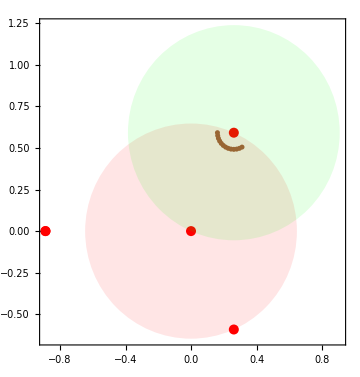

```mathematica
Solve[MirrorCurveDelta2[-27/256,u]==0, u]
Graphics[{PointSize[.02],Red,Point[ReIm/@Join[u/.%,{0}]], Opacity[.1,Red],Disk[ReIm[0],8/(3 √17)], Opacity[.1,Green], Disk[ReIm[up],8/(3 √17)], PointSize[.01],Opacity[1,Brown], Point[ReIm/@(up+points)]},Frame->True,Axes->True,ImageSize->Medium]
```

```mathematica
{b1,b2}=b/.Solve[Thread[KerrDoranElUrFromb[b]=={l0,up}],b]
```

{,}

```mathematica
pf1=Simplify[PicardFuchs2[ff[u],l0,u]/.ff->Function[u,F[u-up]]/.u->z+up];
```

```mathematica
a1=FullSimplify@Together@Coefficient[pf1,Derivative[1][F][z]];
a2=FullSimplify@Together@Coefficient[pf1,Derivative[2][F][z]];
a3=FullSimplify@Together@Coefficient[pf1,Derivative[3][F][z]];
pfop[f_]:=a1 D[f,z]+a2 D[f,{z,2}]+a3 D[f,{z,3}];
```

```mathematica
currentOrder=1;
A0=z;
coeffList={};
MaxTerms=30;
```

```mathematica
Monitor[Do[
var=Symbol["cof"<>ToString[currentOrder+1]];
A0=A0+var z^(currentOrder+1);
limit=Limit[z^(2-currentOrder)pfop[A0], z->0];
sol=FullSimplify[Solve[limit==0,var]];
A0=A0/.First[sol];
AppendTo[coeffList, var/.First[sol]];
currentOrder=currentOrder+1;
, {i, MaxTerms}], ProgressIndicator[i/MaxTerms]]
```

```mathematica
curr=1;
A1=0;
coeffList2={};
MaxTerms=15;
```

```mathematica
powers=z^Range[2,MaxTerms+5];
```

```mathematica
Monitor[Do[
var=Symbol["cofff"<>ToString[curr+1]];
limit=Limit[z^(2-curr)pfop[Log[z](z+coeffList[[;;curr]].powers[[;;curr]])+A1+var z^(curr+1)],z->0];
sol=Solve[limit==0,var];
A1=A1+FullSimplify[var z^(curr+1)/.First[sol]];
AppendTo[coeffList2, FullSimplify[var/.First[sol]]];
curr=curr+1;
, {i, MaxTerms}], ProgressIndicator[i/MaxTerms]]
```

```mathematica
co1=FullSimplify[(b^2+b+1)(b^2+4b+1)^2/(1-b)/(b+1)^5/.b->b2]
co2=FullSimplify[Log[(b^3 (b^2+b+1) (b^2+4 b+1)^2)/(1-b^2)^6]/.{b->b2}]
```

1/16 √(1316+(1817 ⅈ)/(√2))

Log[(6976-11369 ⅈ √2)/110592]

```mathematica
Q0=KerrDoranQ[b2];
```

```mathematica
phi1=co1(z+coeffList[[;;15]].powers[[;;15]]);
phi2=co1(Log[z]phi1+A1)+co1 co2 phi1-4Pi^2 Q0;
```

```mathematica
phi1=z+coeffList[[;;15]].powers[[;;15]];
phi2=Log[z]phi1+A1;
```

```mathematica
Simplify[Series[{pfop[phi1], pfop[phi2]},{z,0,13}]]
```

{O[z]^14,O[z]^14}

```mathematica
ClearAll[a,b,c,d,e,f];
n0=Table[N[{{a,b,c},{d,e,f}}.{1,phi1,phi2}/.{z->p},50], {p,points}];
```

```mathematica
n1=Table[N[{fT[l0,up+p,350,3],fTD[l0,up+p,350,3]},50], {p,points}];
```

```mathematica
Dimensions[n0-n1]
```

{13,2}

```mathematica
sol=First@Solve[Thread[RandomSample[Flatten[n0-n1],6]==0], {a,b,c,d,e,f}]
```

{a→0.3469651370235028831176631083894356215556802435393+0.1656953189836077524721955079731946882275730943282 ⅈ,b→-0.2294190657311805255216449072771085289243225696818+0.05173978273488391767674905306624924547724410658516 ⅈ,c→0.06288074506990312460197818258152689996902646035733+0.02560547376922555869931876992767036571532930975513 ⅈ,d→0.5408954110727213019474865168784530823260011624266+0.4970859569467336199604543243305812370537248539783 ⅈ,e→-0.5273732605853090324718423571665335831300873279511-0.2398720252913251467190256003275229225219514426881 ⅈ,f→0.1886422352373278390112903651659633387790784050273+0.07681642133814384119829531280657458439316992788106 ⅈ}

```mathematica
MatrixForm[N[{{a,b,c},{d,e,f}}/.sol]]
```

(0.346965+0.165695 ⅈ | -0.229419+0.0517398 ⅈ | 0.0628807+0.0256055 ⅈ
0.540895+0.497086 ⅈ | -0.527373-0.239872 ⅈ | 0.188642+0.0768164 ⅈ)

```mathematica
N[-Q0+m0]
```

0.346965+0.165695 ⅈ

```mathematica
N[-3Q0+3m0-1/2]
```

0.540895+0.497086 ⅈ

```mathematica
N[co1/(4Pi^2)]
```

0.0628807+0.0256055 ⅈ

```mathematica
N[co1 (co2-1+Pi I)/(4Pi^2)]
```

-0.229419+0.0517398 ⅈ

```mathematica
N[3co1/(4Pi^2)]
```

0.188642+0.0768164 ⅈ

```mathematica
N[3 co1 (co2-1+Pi I)/(4 Pi^2)-I co1/(2 Pi)]
```

-0.527373-0.239872 ⅈ

```mathematica
cMat1={{-Q+m,c1 (c2-1+Pi I)/(4Pi^2), c1/(4Pi^2)}, {-3Q+3m-1/2, 3 c1 (c2-1+Pi I)/(4 Pi^2)-I c1/(2 Pi), 3c1/(4Pi^2)}};
```

```mathematica
eval={Q->Q0,m->m0,c1->co1,c2->co2};
```

```mathematica
N[(cMat1/.eval)-({{a,b,c},{d,e,f}}/.sol)]
```

{{7.19593×10^-13-1.35956×10^-12 ⅈ,-7.87928×10^-12+2.97518×10^-11 ⅈ,9.23217×10^-12+9.98874×10^-12 ⅈ},{-5.38721×10^-14+1.09557×10^-14 ⅈ,1.06105×10^-12-4.95579×10^-13 ⅈ,7.8034×10^-14-5.00954×10^-13 ⅈ}}

```mathematica
MatrixForm[D[{v0,c1 v1, c1 v2+c1 c2 v1-4Pi^2 Q v0}, {{v0,v1,v2}}]]
```

(1 | 0 | 0
0 | c1 | 0
-4 π^2 Q | c1 c2 | c1)

```mathematica
MatrixForm[Simplify[cMat1]]
```

(m-Q | (c1 (-1+c2+ⅈ π))/(4 π^2) | c1/(4 π^2)
-1/2+3 m-3 Q | (c1 (-3+3 c2+ⅈ π))/(4 π^2) | (3 c1)/(4 π^2))

```mathematica
{{1,0,0,0},{0,1,0,0},{0,1,(-1+I Pi)/(4Pi^2), 1/(4Pi^2)}, {}}
```